```mathematica
hi=Table[Abs[RandomInteger[{1,100}]-RandomInteger[{1,100}]]/2,{i,1,100}]
```

{5/2,85/2,25,17,14,17/2,14,15,83/2,19/2,7,43,21/2,43/2,11/2,13/2,43/2,37/2,5,17/2,3/2,35/2,65/2,25,33/2,38,71/2,35,59/2,77/2,13,7/2,42,8,47/2,3/2,15/2,24,7/2,15/2,26,1,26,17/2,37/2,31/2,5/2,19/2,23/2,1/2,41,41,33/2,31/2,5/2,0,19,1/2,5/2,61/2,21/2,9,5/2,27/2,22,15,30,24,5/2,43/2,61/2,8,11,13,14,4,19/2,17/2,9,49/2,32,51/2,1/2,25/2,53/2,41/2,11/2,29/2,61/2,77/2,11/2,16,27,35/2,57/2,12,1/2,12,1/2,7/2}

{1}
 |  |  |  |

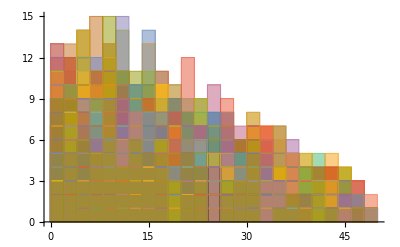

```mathematica
hi=Table[Table[Abs[RandomInteger[{1,100}]-RandomInteger[{1,100}]]/2,{i,1,100}],{j,1,100}]
```

```mathematica
hi[[2]]
```

{1/2,1,1/2,0,0,0,1/2,1,1/2,1,0,1/2,1,1/2,1,1/2,1/2,0,1,0,1/2,0,1/2,0,1,1,1,1,0,1,1,1,0,1/2,1/2,1/2,0,1/2,0,1/2,1/2,1,1/2,1,1/2,1/2,1/2,0,1,1,0,1/2,1,1/2,0,1,0,1,1/2,1/2,1/2,1,1/2,1/2,1/2,1/2,1,1,1/2,1,0,1/2,1/2,1/2,1,1/2,1,0,1,0,1/2,0,0,1/2,1,1,1/2,1/2,1/2,1/2,0,1,1/2,1/2,1/2,1/2,1,1,0,1}

```mathematica
ho=Flatten@hi
```

{9/2,17/2,3,7,14,17,91/2,23/2,29/2,5,9,15/2,17/2,25/2,11/2,25/2,6,8,69/2,2,25/2,85/2,55/2,35/2,9,47,1,33/2,35,21/2,5,2,9,57/2,61/2,39/2,27/2,3,34,13/2,13,6,31,2,93/2,87/2,1/2,39/2,8,9902,45/2,40,10,12,9,1,10,19/2,16,31/2,41/2,77/2,3/2,81/2,1,5,3,7,17/2,12,19/2,1,9/2,22,27/2,53/2,37,15/2,57/2,15,21,9,1/2,29,31,34,27/2,19/2,61/2,31/2,2,26,16,15/2,9,61/2,19/2,43/2,5/2}
 |  |  |  |

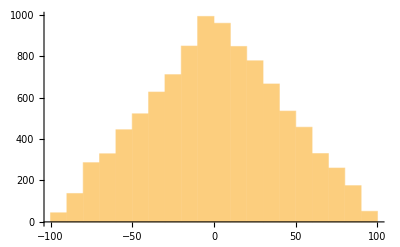

```mathematica
hi=Table[Table[RandomInteger[{1,100}]-RandomInteger[{1,100}],{i,1,100}],{j,1,100}];
ho=Flatten@hi;
Histogram@ho
```

```mathematica
mm ,,,,,,
```